```mathematica
Вариант 3;
```

```mathematica
1. Задаем начальные данные;
Subscript[x, 0] = 0; Subscript[x, 1] = Pi/4; Subscript[x, 2] = Pi/2; n = 2;
f[x_] = Sin[x]^2*Cos[x];
m = 3;
NN = (m + 1)*(n + 1) - 1;
```

```mathematica
2. Строим интерполяционный многочлен Эрмита;
P[x_] = Sum[Subscript[a, k] x^k, {k, 0, NN}];
eqv = Table[(D[P[x], {x, j}] /. x -> Subscript[x, k]) == (D[f[x], {x, j}] /. x -> Subscript[x, k]), {j, 0, m}, {k, 0, n}] // Flatten;
koef = Solve[eqv, {}] // Flatten;
P[x_] = P[x] //. koef // Expand // N[#, 16]&
```

x^2-0.8336508868486672 x^4+0.002308333158932346 x^5+0.2457053828758706 x^6+0.01173278737980559 x^7-0.05178294615415484 x^8+0.005494713478560081 x^9+0.003446201415854223 x^10-0.0006799256305951446 x^11

```mathematica
3. Проверяем выполнение интерполяционных условий;
Table[((D[P[x], {x, j}] /. x -> Subscript[x, k]) - (D[f[x], {x, j}] /. x -> Subscript[x, k]) // Chop) == 0, {j, 0, m}, {k, 0, n}]
```

{{True,True,True},{True,True,True},{True,True,True},{True,True,True}}

```mathematica
4. Контроль через InterpolatingPolynomial;
Tbl = Table[{Subscript[x, i], Table[D[f[x], {x, j}] /. x -> Subscript[x, i], {j, 0, m}]}, {i, 0, n}];
P1[x_] = InterpolatingPolynomial[Tbl, x] // Expand;
N[P[x] - P1[x]] // Chop
```

0

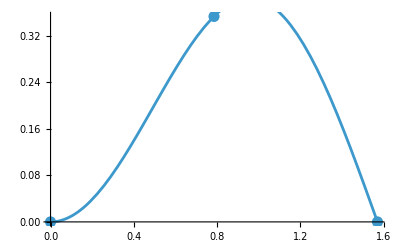

```mathematica
5. Изображаем точки и многочлен;
Tb = Table[{Subscript[x, i], f[Subscript[x, i]]}, {i, 0, n}];
Gr1 = ListPlot[Tb, PlotStyle -> {PointSize[0.02]}];
Gr2 = Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]}];
Show[Gr1, Gr2]
```

```mathematica
6. Оценка погрешности;
M1 = Maximize[{D[f[x], {x, NN + 1}], Subscript[x, 0] <= x <= Subscript[x, n]}, x][[1]];
M2 = Minimize[{D[f[x], {x, NN + 1}], Subscript[x, 0] <= x <= Subscript[x, n]}, x][[1]];
M = Max[{Abs[M1], Abs[M2]}];
omega[t_] = Product[(t - Subscript[x, i])^(m + 1), {i, 0, n}];
Momega = Maximize[{Abs[omega[x]], Subscript[x, 0] <= x <= Subscript[x, n]}, x][[1]];
R = M/((NN + 1)!) * Momega // N
Print["Ответ: оценка погрешности R = ", R]
```

Ответ: оценка погрешности R = 3.35374×10^-7

3.35374×10^-7

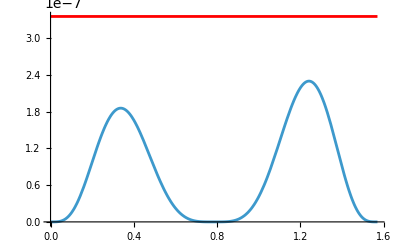

```mathematica
7. Графики абсолютной погрешности и оценки;
Gr3 = Plot[Abs[f[x] - P[x]], {x, Subscript[x, 0], Subscript[x, n]}];
Gr4 = Plot[R, {x, Subscript[x, 0], Subscript[x, n]}, PlotStyle -> Red];
Show[Gr3, Gr4, PlotRange -> Automatic]
```

```mathematica
8. Убеждаемся что погрешность не превосходит оценки;
MR1 = Maximize[{f[x] - P[x], Subscript[x, 0] <= x <= Subscript[x, n]}, x][[1]];
MR2 = Minimize[{f[x] - P[x], Subscript[x, 0] <= x <= Subscript[x, n]}, x][[1]];
MR = Max[{Abs[MR1], Abs[MR2]}];
MR <= R
```

True

```mathematica
9. Проверяем свойство инвариантности;
Unprotect[Power];
0^0 := 1;
Table[Module[{g, Ht}, g[t_] = t^jj; Ht[t_] = InterpolatingPolynomial[Table[{Subscript[x, i], Table[D[g[t], {t, s}] /. t -> Subscript[x, i], {s, 0, m}]}, {i, 0, n}], t]; {t^jj, Expand[g[t] - Ht[t]] === 0}], {jj, 0, NN + 1}]
```

{{1,True},{t,True},{t^2,True},{t^3,True},{t^4,True},{t^5,True},{t^6,True},{t^7,True},{t^8,True},{t^9,True},{t^10,True},{t^11,True},{t^12,False}}